# 28: Basic QR Algorithm

This (with some bells and whistles) is what almost all dense eigenvalue algorithms are based on after a preliminary reduction to upper Hessenberg (tridiagonal for symmetric) form. We are going to look at the scheme first and then work out why it works.

## Motivational Demo

The book says “Compute the QR decomposition, flip the order of the factors and repeat!”. Here is an example for a symmetric matrix.

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergReduction[A]];
TabView[
Table[
{Q,R}=QRDecomposition[T];Q=Qᵀ;
T=Chop[R.Q];
MatrixPlot[T],
{MaxIter}]
]
```

12345678910111213141516171819202122

Lets look at the first and last “T” matrices

```mathematica
TabView[{
"T_0"->MatrixForm[T0],
"T_-1"->MatrixForm[T]}]
Eigenvalues[A]
```

12

{-3.20684,2.84986,-2.11601,1.82991,1.53912,-1.01371,0.52521}

It is pretty clear that something is driving the off-diagonals to zero: this means the diagonals are heading to the eigenvalues!  We want to understand what is doing this. Once we understand that we might be able to make it go faster! In a fit of bravado, we are going to guess at something that makes it go faster

### Shifts

After a few steps I have a vague idea of some of the eigenvalues! There should be a way of incorporating these estimates into the algorithm.

Obvious Fact #42:
If the eigenvalues of A are {λ_1,λ_2,…,λ_m} then the eigenvalues of A-μ I_m are simply {λ_1-μ,λ_2-μ,…,λ_m-μ}
This is called a shift.

Less Obvious Observation:
If μ is an eigenvalue then one QR step on “T-μ I_m" makes the problem gets smaller. 
This is called “Deflation”.

{2.44012,1.28022,-3.86877,-0.179029,-2.72121,-0.905731,-1.56584}

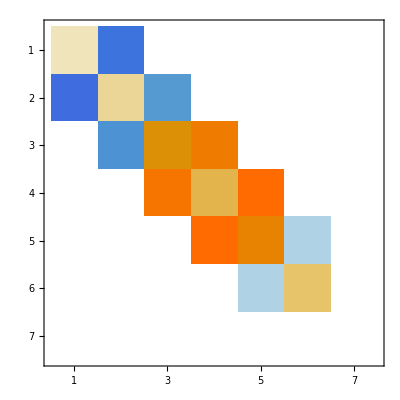

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
λs=Eigenvalues[A];
T0=T=Chop[HessenbergReduction[A]];
μ=RandomChoice[λs];
{Q,R}=QRDecomposition[T-μ IdentityMatrix[m]];Q=Qᵀ;
T=Chop[R.Q];
Eigenvalues[T]+μ
MatrixPlot[T]
```

It does not have to be exact to be useful! The cheesiest guess we have at an eigenvalue is the last diagonal entry! Even this simple “shift” strategy helps a lot.

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
λs=Eigenvalues[A];
T0=T=Chop[HessenbergReduction[A]];
μ=T⟦m,m⟧;
{Q,R}=QRDecomposition[T-μ IdentityMatrix[m]];Q=Qᵀ;
T=Chop[R.Q];
TabView[{
"T_0"->MatrixPlot[T0],
"T_1"->MatrixPlot[T]}]
TabView[{
"T_0"->MatrixForm[T0],
"T_1"->MatrixForm[T]}]
```

12

12

I guess we should throw this into our code and see if it is faster! The one missing ingredient is that we need to add the shift back in if we want to combine steps. Here is our new code!

```mathematica
m=7; MaxIter=4;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergReduction[A]];
Id=IdentityMatrix[m];
TabView[
Table[
μ=T⟦m,m⟧;
{Q,R}=QRDecomposition[T-μ Id];Q=Qᵀ;
T=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
```

1234

(-0.893483 | -2.97 | 0 | 0 | 0 | 0 | 0
-2.97 | 2.29949 | -0.300737 | 0 | 0 | 0 | 0
0 | -0.300737 | 1.07068 | -2.19765 | 0 | 0 | 0
0 | 0 | -2.19765 | 0.223879 | -0.139886 | 0 | 0
0 | 0 | 0 | -0.139886 | 1.98201 | -0.0078356 | 0
0 | 0 | 0 | 0 | -0.0078356 | 0.453441 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.730142)

It almost always immediately resolves an eigenvalue at the bottom corner!  Of course, the shift stops doing any good once that has happened! If we want to continue effectively we need to work out how to “deflate” the converged elements. In general, deflation involves slightly complicated bookkeeping. Our book wimps out on “deflation”. I am going to try to show what happens when the bottom deflates!

### Deflation

Lets decide that the bottom diagonal “eigenvalue” is resolved when the ratio of the off-diagonal element to the diagonal element is less than some tolerance.  Our bookkeeping consists of a single number “n” that is the number of eigenvalues still to be resolved. Of course, n starts at m and the code decreases it as appropriate.

```mathematica
m=8; MaxIter=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergReduction[A]];
(* Initialize the Active Dimension *)
n=m;
Tol=10^-10;
TabView[
Table[
If[ Abs[T⟦n-1,n⟧/T⟦n,n⟧]<Tol,n=n-1] ;
Id=IdentityMatrix[n];
μ=T⟦n,n⟧;
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
Eigenvalues[A]
```

123456789101112

(-4.30069 | 0.44255 | 0 | 0 | 0 | 0 | 0 | 0
0.44255 | 4.15663 | 0.0305438 | 0 | 0 | 0 | 0 | 0
0 | 0.0305438 | -2.6067 | 0.276029 | 0 | 0 | 0 | 0
0 | 0 | 0.276029 | 2.95418 | 0.0258774 | 0 | 0 | 0
0 | 0 | 0 | 0.0258774 | -1.51889 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.340286 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.49397 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.11927)

{-4.32379,4.17987,2.968,-2.6205,-1.51903,1.49397,1.11927,-0.340286}